```mathematica
z:=({{1}, {0}});
e:=({{0}, {1}});
p=({{1/Sqrt[2]}, {1/Sqrt[2]}});
m=({{1/Sqrt[2]}, {-1/Sqrt[2]}});
sigmax:=({{0, 1}, {1, 0}})
sigmaz:=({{1, 0}, {0, -1}})
OnQbit[x_,i_,n_]:=KroneckerProduct[IdentityMatrix[2^(i-1)],x,IdentityMatrix[2^(n-i)]];
State[s_]:=KroneckerProduct@@(If[#≥0,z,e]&/@s);
InitialState[s_]:=1/Sqrt[2]*(State[s]+State[-s]);
Hamilton[F_]:=Sum[Sum[KroneckerProduct[IdentityMatrix[2^(j-1)],F[[l,j]]({{1, 0}, {0, -1}}),IdentityMatrix[2^(Length[F[[l]]]-j)]],{j,1,Length[F[[l]]]}] ,{l,1,Length[F]}];
TimeEvolution[ρinit_,F_,t_]:=Exp[-I*t Hamilton[F]]
TimeEvolutionMasterEquation[ρinit_,F_,L_,γ_,tmax_]:=ρ[tmax]/.NDSolve[
{
ρ'[t]==
-I (Hamilton[F].ρ[t]-ρ[t].Hamilton[F])
+Sum[γ[[j]]*(L[[j]].ρ[t].ConjugateTranspose[L[[j]]]-1/2(ConjugateTranspose[L[[j]]].L[[j]].ρ[t]+ρ[t].ConjugateTranspose[L[[j]]].L[[j]]))
,{j,1,Length[γ]}]
,ρ[0]==ρinit},ρ,{t,0,tmax}]//First
TimeEvolutionSpontaneousEmission[ρinit_,F_,γ_,t_]:=TimeEvolutionMasterEquation[ρinit,F,{OnQbit[z.ConjugateTranspose[e],1,3],OnQbit[z.ConjugateTranspose[e],2,3],OnQbit[z.ConjugateTranspose[e],3,3]},{γ,γ,γ},t];
TimeFlips[s_,t_]:=SortBy[Transpose[{DeleteCases[s,_Integer]*t,Table[i,{i,1,Length[DeleteCases[s,_Integer]]}]}],Abs[First[#]]&]
TimeEvolutionWithFlip[ρinit_,F_,t_,s_,TimeEvolution_]:=Module[{ρTemp,tTemp},
ρTemp=ρinit;
tTemp=0;
For[
i=1,
i<Length[TimeFlips[s,t]],
i++,
ρTemp = TimeEvolution[ρTemp,F,TimeFlips[s,t][[i]]//First-tTemp];
tTemp=TimeFlips[s,t][[i]]//First;
ρTemp=OnQbit[sigmax,TimeFlips[s,t][[i]]//Last,Length[F]].ρTemp.ConjugateTranspose[OnQbit[sigmax,TimeFlips[s,t][[i]]//Last,Length[F]]];
];
Return[TimeEvolution[ρTemp,F,t-tTemp]]]
```

```mathematica
i=2;
F=({{1, 1, 1}, {-1.04, 0, 1.04}, {1.08, 0, 1.08}});
s={0.5,-1,0.5};
ρinit=InitialState[s].ConjugateTranspose[InitialState[s]];
TimeEvolutionSpontaneousEmissionLow[ρinit_,F_,t_]:=TimeEvolutionSpontaneousEmission[ρinit,F,0.1,t];
QFI[t_]:=Module[{ρes,ρfinal,H,QFI},
ρfinal = TimeEvolutionWithFlip[ρinit,F,t,s,TimeEvolutionSpontaneousEmissionLow];
ρes = Transpose[Eigensystem[N[ρfinal]]];
(*Print[ρes];*)
(*Print["Eigensystem Found"];*)
H=t*Sum[KroneckerProduct[IdentityMatrix[2^(j-1)],F[[i,j]]({{1, 0}, {0, -1}}),IdentityMatrix[2^(Length[F[[i]]]-j)]],{j,1,Length[F[[i]]]}];
(*Print["Computing QFI"];*)
QFI=2Sum[If[l[[1]]+j[[1]]==0,0,(l[[1]]-j[[1]])^2/(l[[1]]+j[[1]]) Abs[ConjugateTranspose[Transpose[{l[[2]]}]].H.j[[2]]]^2],{l,ρes},{j,ρes}];
Return[Abs[QFI//First]]];
QFI[1]
```

14.8765

```mathematica
QFI[0.1]
```

0.170477

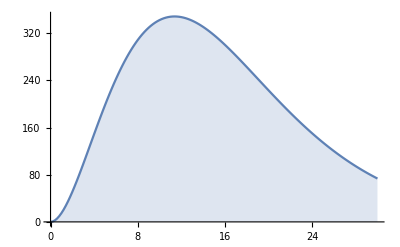

```mathematica
DiscretePlot[QFI[x],{x,0,30,0.2}]
```